{1}

Line[{{{0,0.5},{0,0}}}]

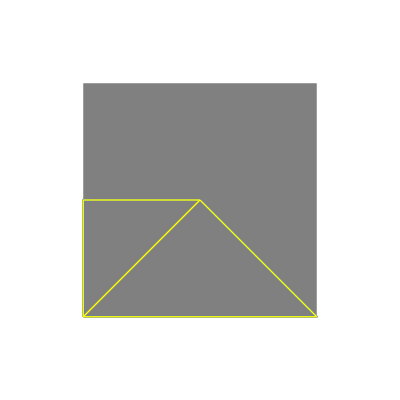

```mathematica
str = OpenRead["~/WM/ICFPC/test"];
npol = ReadList[str,  Number, 1]
For[i=0, i < npol[[1]], i++,
nvert[i] = ReadList[str,Number, 1];
pols[i] = ReadList[str, {Number, Number}, nvert[i][[1]]];
pols[i] = Append[pols[i], pols[i][[1]]];
]

nedg = ReadList[str,  Number, 1];
For[i=0, i < nedg[[1]], i++,
edgs[i] = Line[ReadList[str, {{Number, Number}, {Number, Number}}, 1]];
]
edgs[3]
gedgs=Table[Graphics[{Yellow,Thick, edgs[i]}], {i, 0, nedg[[1]]-1}];

bd = 0.2;
Show[Graphics[{Thin, Dashed, Gray,Rectangle[]}],ListLinePlot[pols[0]],gedgs,
 PlotRange->{{-bd, 1+bd}, {-bd, 1+bd}}, AspectRatio->1]
```